La funzione da calcolare è:

(√3-2 x-Log[35])/(2 x)

I contenuti sotto radice pari

{3}

devono essere maggiori di zero:

{True}

I contenuti sotto logaritmi

{35}

devono essere maggiori di zero:

{True}

Il denominatore:

{2 x}

deve essere diverso di zero:

{x>0,x<0}

quindi facendo l'intersezione tra questi domini, il dominio è:

x<0||x>0

La funzione non è pari.

La funzione non è dispari.

Per scoprire dove interseca l'asse x poniamo il numeratore = 0:

√3-2 x-Log[35]==0

che risulta:

x==1/2 (√3-Log[5]-Log[7])

Per scoprire dove interseca l'asse y, calcoliamo f(x) con x=0 se il dominio lo ammette e otteniamo che interseca l'asse y in

y==√3-Log[35]

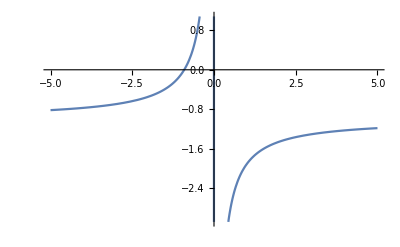

x==1/2 (√3-Log[5]-Log[7])

Per scoprire dove interseca l'asse y, calcoliamo f(x) con x=0 se il dominio lo ammette e otteniamo che interseca l'asse y in

IntersezioneAssi`Private`y==√3-Log[35]

-Graphics-

```mathematica
$IterationLimit=$RecursionLimit=50;

Get["Desktop/Progetto Matematica Computazionale/dominio.m"]
Get["Desktop/Progetto Matematica Computazionale/paridispari.m"]
Get["Desktop/Progetto Matematica Computazionale/segno.m"]
Get["Desktop/Progetto Matematica Computazionale/derivata.m"]
Get["Desktop/Progetto Matematica Computazionale/grafico.m"]
Get["Desktop/Progetto Matematica Computazionale/intersezioneassi.m"]

Print["La funzione da calcolare è: "]
f[x_]:=(Sqrt[3]-2*x-Log[35])/(2*x);
f[x]
(* x-Sqrt[x^2-1]
(x^2)^(1/2)*e^x
(Sqrt[3]-2*var-Log[35])/(2*var)
(e^x-1)/x
(2*x-1)/(x*e^x)
(e^Tan[x]-1)/(e^Tan[x]+1)
(x*(x-1)^2)/(x+1)^2
2^(x+1/x)
x/(e^x-1)
x^2/2-x+Log[x+1]
*)
fDivisa= DividiFunzioneInListaDiOperandi[f[x]];

Print["I contenuti sotto radice pari "]
listaContenutiRadiciDaControllare={};
CalcolaContenutiRadiciDaControllare[listaContenutiRadiciDaControllare,#]&/@fDivisa;
listaContenutiRadiciDaControllare
Print[" devono essere maggiori di zero: "];
risultatoControlloRadici={};
risultatoControlloRadici=Reduce[#>0,x]&/@listaContenutiRadiciDaControllare;
DeleteCases[risultatoControlloRadici,True];
risultatoControlloRadici

Print["I contenuti sotto logaritmi "]
listaContenutiLogaritmoDaControllare ={};
CalcolaContenutiLogaritmoDaControllare[listaContenutiLogaritmoDaControllare,#]&/@fDivisa;
listaContenutiLogaritmoDaControllare
Print[" devono essere maggiori di zero: "];
risultatoControlloLogaritmo={};
risultatoControlloLogaritmo=Reduce[#>0,x]&/@listaContenutiLogaritmoDaControllare;
DeleteCases[risultatoControlloLogaritmo,True];
risultatoControlloLogaritmo

listaContenutiDenominatoreDaControllare = {};
risultatoControlloDenominatore={};
Print["Il denominatore: "]
listaContenutiDenominatoreDaControllare = Append[listaContenutiDenominatoreDaControllare,Denominator[f[x]]]
Print[" deve essere diverso di zero: "];
CalcolaContenutiDenominatoreDaControllare[risultatoControlloDenominatore,listaContenutiDenominatoreDaControllare];
DeleteCases[risultatoControlloDenominatore,True];
risultatoControlloDenominatore

Print["quindi facendo l'intersezione tra questi domini, il dominio è: "]
dominio = FunctionDomain[f[x],x]

ControlloPariDispari[f,x]

ControlloIntersezioneAssi[f,x]

SegnoFunzione[f,x]

(*SegnoDerivataPrima[f,x]*)
GraficoFunzione[f,x,-5,5]
```